{0.991182,0.991182,3.99196,3.99196,8.99246,8.99246,16.0244,16.0244}

{4,3.99196}

{0.9911,0.9911,3.99112,3.99112,8.99112,8.99112,15.9911,15.9911,24.9911,24.9911,35.9911,35.9911,48.9911,48.9911,63.9911,63.9911,80.9911,80.9911,99.9911,99.9911,120.991,120.991,143.991,143.991,168.991,168.991,195.991,195.991,224.991,224.991,255.991,255.991,288.991,288.991,323.991,323.991,360.991,360.991,399.991,399.991,440.991,440.991,483.991,483.991,528.991,528.991,575.991,575.991,624.991,624.991,675.991,675.991,728.991,728.991,783.992,783.992,840.992,840.992,899.992,899.992,960.992,960.992,1023.99,1023.99,1088.99,1088.99,1155.99,1155.99,1224.99,1224.99,1296.,1296.,1369.,1369.,1444.01,1444.01,1521.01,1521.01,1600.3,1600.3}

{0.9911,3.99112,8.99112,15.9911,24.9911,35.9911,48.9911,63.9911,80.9911,99.9911,120.991,143.991,168.991,195.991,224.991,255.991,288.991,323.991,360.991,399.991,440.991,483.991,528.991,575.991,624.991,675.991,728.991,783.992,840.992,899.992,960.992,1023.99,1088.99,1155.99,1224.99,1296.,1369.,1444.01,1521.01,1600.3}

{3.00002,5.,7.,9.,11.,13.,15.,17.,19.,21.,23.,25.,27.,29.,31.,33.,35.,37.,39.,41.,43.,45.,47.,49.,51.0001,53.,55.0001,57.,59.0002,61.,63.0004,65.,67.0008,69.0001,71.0023,73.0001,75.0106,77.0006,79.2912}

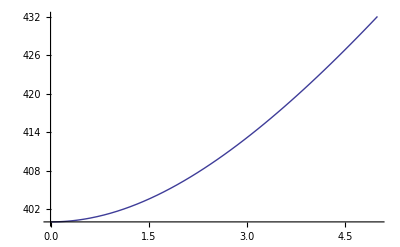

```mathematica
(*Matrix for first order perturbation, accounting for spin - all energy eigenvalues are doubly degenerate*)

Clear[mixingAmplitude, energy, eigen, numStates, eigenTable,eigenTablePlot, α, length, matrixSizeToUse, temp, t]

eigen[maxEnergy_, mixingStrength_, length_]:=Module[
{
maxEn = maxEnergy, (*max energy level to include*)
len = length, (*Length of box*)
α =  mixingStrength, (*strength of the mixing*)
matrix = IdentityMatrix[2*maxEnergy]
},
mixingAmplitude[n_,m_] := α/len(2n m ((-1)^(m+n) -1))/Abs[m^2-n^2] ⅈ;(*The abs just a sign adjustment - change back later?*)
sign[i_]:=If[Mod[i,2]==0,1,-1];
energy[n_]:= n^2 ;
Do[
matrix[[i,i]]=energy[(i+1)/2];
matrix[[i+1,i+1]]=energy[(i+1)/2];
,
{i,1, 2maxEn, 2}
];
Do[
If[
i≠j && Mod[Floor[i/2],2]==Mod[Floor[j/2],2],
matrix[[i,j]]=sign[i]*mixingAmplitude[Ceiling[i/2],Ceiling[j/2]];
];
,
{i,1, 2maxEn, 1},
{j,1, 2maxEn, 1}
];
Re[N[Eigenvalues[matrix]]]
]

matrixSizeToUse[energyLevel_, precision_,maxIterations_, alpha_, length_]:=Module[
{
count = energyLevel
},
en1=Sort[eigen[count, alpha, length]][[2energyLevel]];
en2=Sort[eigen[count+1, alpha, length]][[2energyLevel]];
While[
count<maxIterations && Abs[en2 - en1] > precision ,
count++;
en1 = en2;
en2 = Sort[eigen[count+1, alpha, length]][[2energyLevel]];
];
{count+1, en2}
]
 
numStates=8;
length = 5;
α = 0.3;

Sort[eigen[4,α,length]]
matrixSizeToUse[2, .0001, 25,α,length]
(*Do[Print[Sort[eigen[i,α,length]]],{i,10}]

eigen[40,α,length]
eigenTable=Table[{n,eigen[n,α,length]},{n,numStates}];
eigenTablePlot=Flatten[
Table[{eigenTable[[n,1]],eigenTable[[n,2,i]]},
{n,numStates},
{i,1,Length[eigenTable[[n,2]]]}
],
1
];
ListPlot[
eigenTablePlot
]
*)
temp = Sort[eigen[40,α,length]]
t = Table[temp[[2i-1]],{i,1,Floor[Length[temp]/2]}](*unique eigenvalues*)
Differences[t]

Plot[eigen[20, a, length][[1]],{a,0,5}]
```

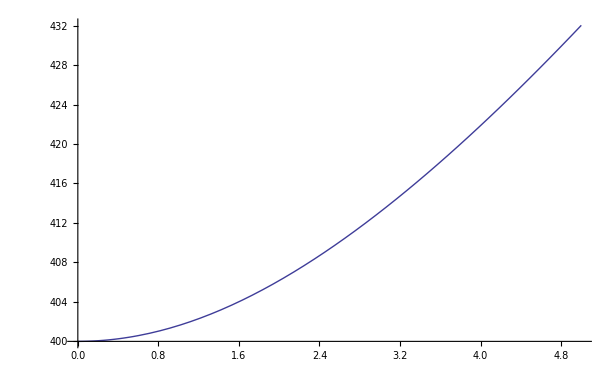
```mathematica
(*x axis is alpha, y axis is lowest energy level*)
-Graphics-
```

```mathematica
Clear[L,n,m]
Refine[Integrate[(2 m π)/L^2 Sin[(n π x)/L]Cos[(m π x)/L],{x,0,L}],n∈Integers&&m∈Integers]
```

(2 m (-n+(-1)^(m+n) n))/(L (m^2-n^2))

```mathematica
Refine[Integrate[n*π*Sin[m π x]Cos[n π x],{x,0,1}],n∈Integers&&m∈Integers]
```

((-m+(-1)^(m+n) m) n)/(-m^2+n^2)

```mathematica
Get["Eigen`"]
Clear[test, L, α];
L = 5;
α=2;

test=EigenNDSolve[{
y''[x]+α ⅈ z'[x]==-ω y[x],
z''[x]-α ⅈ y'[x]==-ω z[x],
y[0]==0,y[L]==0,
z[0]==0,z[L]==0},

{y,z},
{x,0,L},
ω,
Npoly->20,
precision->15
];
Sort[Re[test[[1]]]]
```

{1.394783991,1.394784176,2.579136712,2.579136876,4.553057367,4.553057613,7.316546279,7.316546817,10.86960416,10.86960476,15.2122308,15.21223085,20.34442176,20.34442201,26.26622681,26.26622691,32.97764071,32.97764125,40.48266245,40.48266429,48.56922232,48.56922437,57.46928626,57.46928729,66.17475379,66.17475401,86.36359694,86.3635971,103.006771,103.0067713,165.9925467,165.992547,200.2794381,200.2794383,514.4150628,514.4150631,625.3142485,625.3142486,9399.448304,9399.448305,11387.61045,11387.61045}

```mathematica
(*List of energy eigenvalues with 40 energy levels - 80x80 matrix*)
{1612.1710680497922,1612.1710680497922,1522.5334405339988,1522.5334405339988,1444.017457350959,1444.017457350959,1368.9019215042447,1368.9019215042447,1295.742350377384,1295.742350377384,1224.7162860670169,1224.7162860670169,1155.6713331803392,1155.6713331803392,1088.661364096198,1088.661364096198,1023.6430311897336,1023.6430311897336,960.6381503978415,960.6381503978415,899.6290360809987,899.6290360809987,840.6262732812777,840.6262732812777,783.6211479694816,783.6211479694816,728.6194267218578,728.6194267218578,675.6162937376357,675.6162937376357,624.6151459914536,624.6151459914536,575.6131133002049,575.6131133002049,528.6123084723663,528.6123084723663,483.61093049324603,483.61093049324603,440.6103441519317,440.6103441519317,399.6093789312217,399.6093789312217,360.6089391224682,360.6089391224682,323.60824649076864,323.60824649076864,288.60790931824664,288.60790931824664,255.607403785937,255.607403785937,224.60714133717536,224.60714133717536,195.60676855697272,195.60676855697272,168.60656252647743,168.60656252647743,143.6062867729354,143.6062867729354,120.606124911767,120.606124911767,99.60592206954131,99.60592206954131,80.60579612578286,80.60579612578286,63.605649592334636,63.605649592334636,48.60555408202685,48.60555408202685,35.605452288971236,35.605452288971236,24.605383754851797,24.605383754851797,15.60531862821751,15.60531862821751,8.605275202538133,8.605275202538133,3.6052411907718698,3.6052411907718698,0.6052223630318324,0.6052223630318324}
```